```mathematica
plotThemes={"Default","Monochrome"};
```

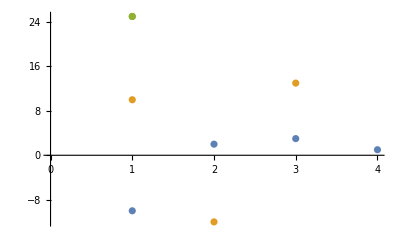
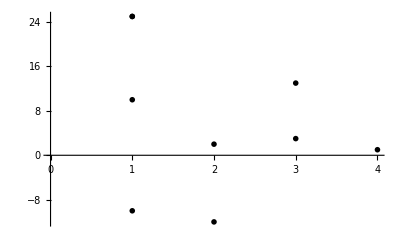

```mathematica
Table[ListPlot[{{-10,2,3,1},{10,-12,13},{25}},PlotTheme->i],{i,plotThemes}]
```

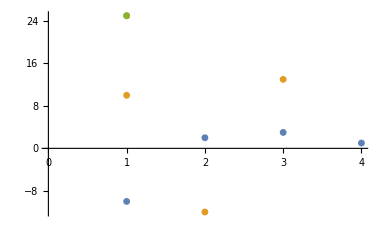
```mathematica
-Graphics-//Rasterize
```

```mathematica
TextRecognize[-Graphics-]
```

ED

```mathematica
DominantColors[-Graphics-,2]//Last
```

RGBColor[0.3686265049386595, 0.505882043771485, 0.7098030258061783]

```mathematica
DominantColors[-Graphics-,2]//Last
```

RGBColor[0.8823536948681678, 0.6117636099154456, 0.14117669136615543]

```mathematica
FindClusters[{RGBColor[0.8823536948681678, 0.6117636099154456, 0.14117669136615543]->{3,7},RGBColor[0.8823536948681678, 0.6117636099154456, 0.14117669136615543]->{1,5},RGBColor[0.8823536948681678, 0.6117636099154456, 0.14117669136615543]->{6,5},RGBColor[0.3686265049386595, 0.505882043771485, 0.7098030258061783]->{7,6},RGBColor[0.3686265049386595, 0.505882043771485, 0.7098030258061783]->{7,10},RGBColor[0.3686265049386595, 0.505882043771485, 0.7098030258061783]->{9,8},RGBColor[0.3686265049386595, 0.505882043771485, 0.7098030258061783]->{7,4}}]
```

{{{3,7},{1,5},{6,5}},{{7,6},{7,10},{9,8},{7,4}}}

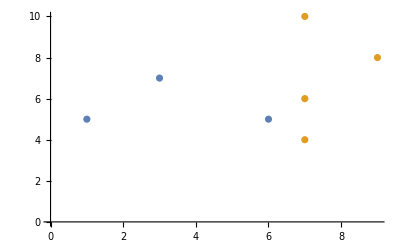

```mathematica
ListPlot@FindClusters[{RGBColor[0.8823536948681678, 0.6117636099154456, 0.14117669136615543]->{3,7},RGBColor[0.8823536948681678, 0.6117636099154456, 0.14117669136615543]->{1,5},RGBColor[0.8823536948681678, 0.6117636099154456, 0.14117669136615543]->{6,5},RGBColor[0.3686265049386595, 0.505882043771485, 0.7098030258061783]->{7,6},RGBColor[0.3686265049386595, 0.505882043771485, 0.7098030258061783]->{7,10},RGBColor[0.3686265049386595, 0.505882043771485, 0.7098030258061783]->{9,8},RGBColor[0.3686265049386595, 0.505882043771485, 0.7098030258061783]->{7,4}}]
```

```mathematica
ListPlot
```

{{{3,7},{1,5},{6,5}},{{7,6},{7,10},{9,8},{7,4}}}

## Functions used

```mathematica
ClearAll["Global`*"];
```

```mathematica
theme = "Default";
(* Generate ranges*)
ranges[max_Integer, di_Integer]:= Flatten[Table[{{-100 + i, 0 + i},{-100 + j, 0 + j}},{i, 0, 100, 10},{j, 0, max, di}], 1]


(* generating random 2D points for the plots *)
getRandomPointsList[nPoints_Integer, ranges_] := ParallelMap[ Partition[ Transpose@{RandomReal[ First[#], nPoints],RandomReal[ Last[#], nPoints]}, Round[nPoints/5]]&, ranges]


(* generating corresponding scattered plots as images *)
getRasterizedPlots[data_,ranges_] := ParallelMap[Rasterize[ListPlot[First[#],PlotRange->Last[#],PlotTheme->theme], ImageSize->{360,240} ] &, Transpose[{data,ranges}]]


(* extracting raw axes from scattered plots *)
getRawAxes[data_,ranges_] := ParallelMap[AlphaChannel[Rasterize[ListPlot[First[#],PlotRange->Last[#],PlotStyle->Transparent,LabelStyle->Transparent,BaseStyle->{Antialiasing->False},PlotTheme->theme],Background->None,ImageSize->{360,240}]]&, Transpose[{data,ranges}] ]

(* extracting raw laberls from scattered plots*)
getRawLabels[data_,axes_,ranges_] := MapThread[ImageDifference[Binarize[AlphaChannel[Rasterize[ListPlot[#1, PlotRange-> #3, PlotStyle->Transparent, BaseStyle->{Antialiasing->False},PlotTheme->theme], Background->None, ImageSize->{360,240}]],0],#2]&,
{data, axes, ranges}
]

(* generating binarized points from scattered plots *)
getBinarizedPoints[data_,ranges_]:= ParallelMap[AlphaChannel[Rasterize[ListPlot[First[#], PlotRange->Last[#], AxesStyle->Transparent, BaseStyle->{Antialiasing->False},PlotTheme->theme], Background->None, ImageSize->{360,240}]]&, Transpose[{data,ranges}]]


(* filtering out points that are overlapping with the axes and axes labels *)
getAxes[axes_, binarizedPoints_]:= MapThread[ImageSubtract[#1, #2]&,{axes, binarizedPoints}]

getLabels[binarizedPoints_, labels_]:= MapThread[ImageSubtract[#1, #2]&,{labels, binarizedPoints}]

(* generating backgrounds from scattered plots *)
getBackgrounds[axes_,labels_,binarizedPoints_]:= MapThread[ColorNegate[ImageAdd[#1,#2,#3]]&,{axes,labels,binarizedPoints}]


(* generating image segmentations from scattered plots *)
segmentateImage[background_,axes_,labels_,binarizedPoints_]:= Round[ImageData[ImageAdd@@MapThread[ImageMultiply,{Image[{background, axes, labels, binarizedPoints},"Real32"],{1,2,3,4}}]]]

getSegmentations[dataPoints_,ranges_]:=Module[{r=ranges,data=dataPoints, binarizedPoints, axes, labels, backgrounds},
binarizedPoints=getBinarizedPoints[data,r];
axes=getAxes[getRawAxes[data,r], binarizedPoints];
labels=getLabels[binarizedPoints, getRawLabels[data, axes,r]];
backgrounds=getBackgrounds[axes, labels, binarizedPoints];
MapThread[segmentateImage[#1, #2, #3, #4]&,{backgrounds, axes, labels, binarizedPoints}]
]

(* generating training data where scattered plots are used as inputs and image segmentations are used as outputs *)
createTrainingData[max_,di_,nPoints_Integer] := Module[{ranges=ranges[max,di], data, plotsImages, segmentations},
data=getRandomPointsList[nPoints,ranges];
plotsImages= getRasterizedPlots[data,ranges];
segmentations = getSegmentations[data,ranges];
MapThread[Rule[#1, #2]&,{plotsImages, segmentations}]
]
```

```mathematica
createTrainingData[100,10,50]
```

```mathematica
monochromeThemePlots=Flatten@Table[createTrainingData[100,10,50],100];
```

```mathematica
defaultThemePlots=Flatten@Table[createTrainingData[100,10,50],100];
```

```mathematica
SeedRandom[1234];
data=RandomSample[Join[monochromeThemePlots,defaultThemePlots]
```

```mathematica
plotsDefault=createTrainingData[20,10,50]
```

{-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1},-Graphics-→{1}}
 |  |  |  |

```mathematica
plots[[1,2]]//Colorize
```

-Graphics-

```mathematica
MinMax[plots[[1,2]]]
```

{1,4}

```mathematica
getRasterizedPlot[nPoints_Integer,xRange_,yRange_] := Rasterize[ListPlot[Partition[ Transpose@{RandomReal[ xRange, nPoints],RandomReal[ yRange, nPoints]}, Round[nPoints/5]],PlotRange->{xRange,yRange}], ImageSize->{360,240}]
```

```mathematica
getRasterizedPlot[100,{-50,50},{-10,50}]
```

-Graphics-

Generates ranges:

```mathematica
Clear[ranges]
```

```mathematica
ranges[max_Integer,di_Integer]:=Flatten[Table[{{-100+i,0+i},{-100 +j,0+j}},{i,0,100,10},{j,0,max,di}],1]
```

```mathematica
ranges=Flatten[Table[{{-100+i,0+i},{-100 +j,0+j}},{i,0,100,10},{j,0,100,10}],1];
```

```mathematica
ParallelMap[getRasterizedPlot[100,First@#,Last@#]&,ranges]//AbsoluteTiming
```

### other old functions

```mathematica
Table[getRasterizedPlot[100,{-100+i,0+i},{-100 +j,0+j}],{i,0,100,10},{j,0,100,10}]//AbsoluteTiming
```

```mathematica
getRasterizedPlots[nPoints_Integer,nPlots_Integer] := MapIndexed[Rasterize[ListPlot[Partition[ Transpose@{RandomReal[ {-90,110}, #],RandomReal[ {0,100}, 20]}RandomReal[ #1, {nPoints,2}], Round[nPoints/5]],PlotRange->{{-50+10First[#2],50+10First[#2]},{-50,50}}], ImageSize->{360,240}] &, Table[{-100 +10i, 100 +10 i},{i,0,nPlots}]]
```

```mathematica
getRasterizedPlots[20,5]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

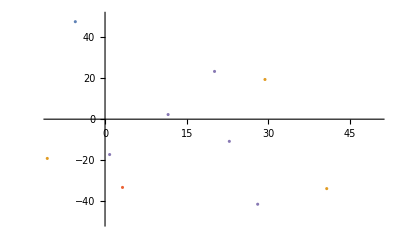

```mathematica
ListPlot[First@getRandomPointsList[{-500,500},1500,5],PlotRange->{{-10,50},{-50,50}}]
```

```mathematica
,
```

```mathematica
Part[createTrainingData[50,50,1],1,2]//Colorize
```

-Graphics-

```mathematica
RotationTransform[Part[createTrainingData[50,50,1],1,2],90]//Colorize
```

```mathematica
Rotate
```